```mathematica
ClearAll["`*"]
$PreRead=(#/.
s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`15."&);
```

```mathematica
order = 3;
kmin = 0.1; R = 10; Z=2; c = 137.036; k =-1;
nnode = 10;
knot = Table[ kmin(R/kmin)^((i-1)/(nnode-1)), {i,1, nnode}]
n = Length[knot]-order-2
ϕi[r_, i_] := BSplineBasis[{order,knot},i, r]
v=-Z/r;
```

{0.1,0.16681005372001,0.27825594022071,0.46415888336128,0.77426368268113,1.2915496650149,2.1544346900319,3.5938136638046,5.9948425031894,10.}

5

```mathematica
Cmat =  Evaluate[Table[Integrate[ϕi[r,ai] ϕi[r,aj],{r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Cmat // Dimensions, SymmetricMatrixQ[Cmat]}
Cmat // MatrixForm
```

{{4,4},True}

(0.13689018203939 | 0.082369512646933 | 0.0091566816443596 | 0.000081089903728316
0.082369512646933 | 0.22834658619733 | 0.13740062829526 | 0.015274265569926
0.0091566816443596 | 0.13740062829526 | 0.38090506310356 | 0.22919806187094
0.000081089903728316 | 0.015274265569926 | 0.22919806187094 | 0.63538794038527)

```mathematica
Dmat =  Evaluate[Table[Integrate[ϕi[r,ai] D[ϕi[r,aj], r],{r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Dmat // Dimensions, SymmetricMatrixQ[Dmat]}
Dmat // MatrixForm
```

{{4,4},False}

(-1.9752731587315×10^-15 | 0.3530556461617 | 0.071826193810725 | 0.0010973220722845
-0.3530556461617 | 1.5581515151206×10^-15 | 0.3530556461617 | 0.071826193810725
-0.071826193810726 | -0.3530556461617 | -1.5437050454253×10^-15 | 0.3530556461617
-0.0010973220722845 | -0.071826193810725 | -0.3530556461617 | 8.4680014371373×10^-16)

```mathematica
Vmat = Evaluate[Table[Integrate[ϕi[r,ai] v ϕi[r,aj], {r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Vmat // Dimensions, SymmetricMatrixQ[Vmat]}
N[Vmat, 12] // MatrixForm
```

{{4,4},True}

(-0.502587267983 | -0.238602331893 | -0.0216314842475 | -0.00015812608857
-0.238602331893 | -0.502587267983 | -0.238602331893 | -0.0216314842475
-0.0216314842475 | -0.238602331893 | -0.502587267983 | -0.238602331893
-0.00015812608857 | -0.0216314842475 | -0.238602331893 | -0.502587267983)

```mathematica
Kmat = Evaluate[Table[Integrate[ϕi[r,ai] k/r ϕi[r,aj],{r,0,R}], {ai,1,n-1}, {aj,1,n-1}]];
{Kmat // Dimensions, SymmetricMatrixQ[Kmat]}
Kmat // MatrixForm
```

{{4,4},True}

(-0.25129363399149 | -0.11930116594665 | -0.010815742123768 | -0.000079063044284978
-0.11930116594665 | -0.25129363399149 | -0.11930116594665 | -0.010815742123768
-0.010815742123768 | -0.11930116594665 | -0.25129363399149 | -0.11930116594665
-0.000079063044284978 | -0.010815742123768 | -0.11930116594665 | -0.25129363399148)

```mathematica
Aprime = Table[If[k > 0, 
2 c^2 KroneckerDelta[i,1]KroneckerDelta[j,1]- c/2 KroneckerDelta[i,1]KroneckerDelta[j,n]- c/2 KroneckerDelta[i,n]KroneckerDelta[j,1]+ c/2 KroneckerDelta[i,n-1]KroneckerDelta[j,n-1]- c/2 KroneckerDelta[i,2n-2]KroneckerDelta[i,2n-2],
c KroneckerDelta[i,1]KroneckerDelta[j,1]- c/2 KroneckerDelta[i,1]KroneckerDelta[j,n]- c/2 KroneckerDelta[i,n]KroneckerDelta[j,1]+ c/2 KroneckerDelta[i,n-1]KroneckerDelta[j,n-1]- c/2 KroneckerDelta[i,2n-2]KroneckerDelta[j,2n-2]
],{i,1,2n-2},{j,1,2n-2}];
{Aprime // Dimensions, SymmetricMatrixQ[Aprime]}
Aprime // MatrixForm
```

{{8,8},True}

(137.036 | 0 | 0 | 0 | -68.518 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 68.518 | 0 | 0 | 0 | 0
-68.518 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -68.518)

```mathematica
Amat = ArrayFlatten[{{Vmat, c (Dmat-Kmat)}, {-c(Dmat+Kmat), Vmat-2c^2 Cmat}}] + Aprime;
{Amat // Dimensions, SymmetricMatrixQ[Amat]}
N[Amat, 15] //MatrixForm //ScientificForm
```

{{8,8},True}

(1.36533412732017×10^2 | -2.38602331893308×10^-1 | -2.16314842475362×10^-2 | -1.58126088569956×10^-4 | -3.4081725572343×10^1 | 6.4729888104080×10^1 | 1.13249203327193×10^1 | 1.61207110834218×10^-1
-2.38602331893308×10^-1 | -5.0258726798297×10^-1 | -2.38602331893307×10^-1 | -2.16314842475361×10^-2 | -3.2032778950749×10^1 | 3.4436274427657×10^1 | 6.4729888104080×10^1 | 1.13249203327192×10^1
-2.16314842475362×10^-2 | -2.38602331893307×10^-1 | -5.0258726798297×10^-1 | -2.38602331893308×10^-1 | -8.3606282573739 | -3.2032778950748×10^1 | 3.4436274427657×10^1 | 6.4729888104080×10^1
-1.58126088569956×10^-4 | -2.16314842475361×10^-2 | -2.38602331893308×10^-1 | 6.80154127320170×10^1 | -1.39538144160945×10^-1 | -8.3606282573738 | -3.2032778950749×10^1 | 3.4436274427657×10^1
-3.4081725572342×10^1 | -3.2032778950749×10^1 | -8.3606282573739 | -1.39538144160945×10^-1 | -5.1417871649934×10^3 | -3.0938505673197×10^3 | -3.4392581379982×10^2 | -3.0457108840479
6.4729888104080×10^1 | 3.4436274427657×10^1 | -3.2032778950748×10^1 | -8.3606282573739 | -3.0938505673197×10^3 | -8.5766821532701×10^3 | -5.1606943830166×10^3 | -5.7368838275019×10^2
1.13249203327193×10^1 | 6.4729888104080×10^1 | 3.4436274427657×10^1 | -3.2032778950749×10^1 | -3.4392581379982×10^2 | -5.1606943830166×10^3 | -1.43064323284403×10^4 | -8.6083976622893×10^3
1.61207110834218×10^-1 | 1.13249203327192×10^1 | 6.4729888104080×10^1 | 3.4436274427657×10^1 | -3.0457108840479 | -5.7368838275019×10^2 | -8.6083976622893×10^3 | -2.39327496736638×10^4)

```mathematica
Bmat = ArrayFlatten[{{Cmat,0}, {0,Cmat}}];
{Bmat // Dimensions, SymmetricMatrixQ[Bmat]}
N[Bmat, 15] //MatrixForm //ScientificForm
```

{{8,8},True}

(1.36890182039395×10^-1 | 8.2369512646933×10^-2 | 9.1566816443596×10^-3 | 8.1089903728316×10^-5 | 0 | 0 | 0 | 0
8.2369512646933×10^-2 | 2.28346586197327×10^-1 | 1.37400628295256×10^-1 | 1.52742655699261×10^-2 | 0 | 0 | 0 | 0
9.1566816443596×10^-3 | 1.37400628295256×10^-1 | 3.80905063103562×10^-1 | 2.29198061870942×10^-1 | 0 | 0 | 0 | 0
8.1089903728316×10^-5 | 1.52742655699261×10^-2 | 2.29198061870942×10^-1 | 6.3538794038527×10^-1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.36890182039395×10^-1 | 8.2369512646933×10^-2 | 9.1566816443596×10^-3 | 8.1089903728316×10^-5
0 | 0 | 0 | 0 | 8.2369512646933×10^-2 | 2.28346586197327×10^-1 | 1.37400628295256×10^-1 | 1.52742655699261×10^-2
0 | 0 | 0 | 0 | 9.1566816443596×10^-3 | 1.37400628295256×10^-1 | 3.80905063103562×10^-1 | 2.29198061870942×10^-1
0 | 0 | 0 | 0 | 8.1089903728316×10^-5 | 1.52742655699261×10^-2 | 2.29198061870942×10^-1 | 6.3538794038527×10^-1)

```mathematica
energy = Sort[Eigenvalues[N[{Amat, Bmat},30]]] // ScientificForm
```

{-3.7706744185245×10^4,-3.7572471309802×10^4,-3.7561693562717×10^4,-3.7560216777576×10^4,-5.2053078647871×10^-1,2.5911450449104,1.45281276207252×10^2,1.37107659851098×10^3}

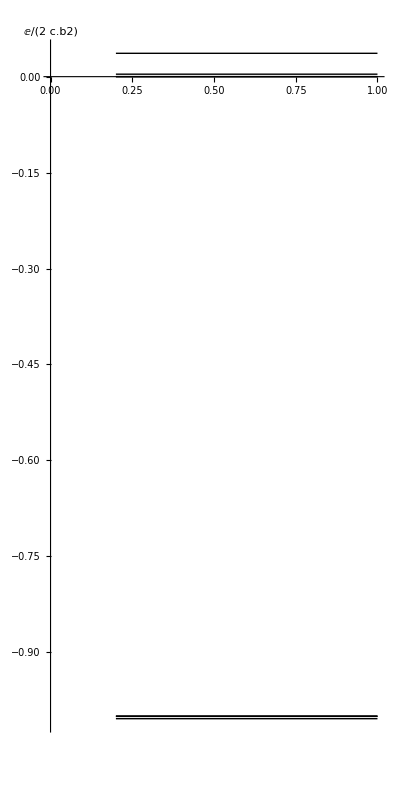

```mathematica
Plot[energy/(2 c^2),{x,.2,1},PlotStyle->{{Thin, Black}},Axes->{False,True},AspectRatio->2,PlotRange->{{0,1},Automatic}, AxesLabel->E/(2 c.b2)]
```

#### Plot Fortran result

-Graphics-

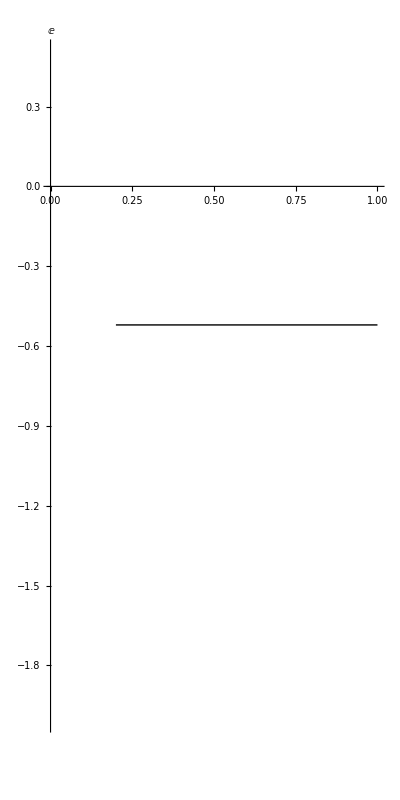

```mathematica
feigval =Import["/home/mathispanet/Documents/Dirac_Equation/eigenvalues.dat", "CSV"];
Plot[feigval/(2 c^2),{x,.2,1},PlotStyle->{{Thin, Black}},Axes->{False,True},AspectRatio->2,PlotRange->{{0,1},Automatic}, AxesLabel->E/(2 c.b2)]
Plot[feigval,{x,.2,1},PlotStyle->{{Thin, Black}},Axes->{False,True},AspectRatio->2,PlotRange->{{0,1},{-2, 0.5}},PlotRangeClipping->True, AxesLabel->E]
```

#### Analytical Solution

```mathematica
m  =1; c = 137.035989; Z=2; kappa=-1; n=1;
(m c^2)/(√(1+((Z/c)/(n - Abs[kappa]+√(kappa^2-(Z/c)^2)))^2))-m c^2
```

-2.000106514